FittedModel[Piecewise[{{-0.133522+0.00192172 x, x<288.}, {-3.79323+0.0000457803 x^2, x≥288.}, {0, True}}]]

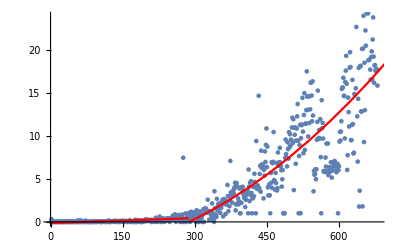

0.839389

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "comma"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, Piecewise[{{a+b*x,x<e},{c+d*x^2,x>=e}}],{a,b,c,d,{e,288}},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```